#### Computation of a*=f(N)

Actually, the second solution would just gives a off result over the whole plane, which is not physically relevant.

#### 1) 1st method using discriminant

```mathematica
ClearAll[a,kb,ka,mu,eta,lambdaa,lambdab,n,astar];

g[a_,n_]:=kb*μ*a^3+(μ+kb*η)a^2+(η-λb-kb*N)a-n
```

```mathematica
poly=Expand[g[a,n]];
poly//TraditionalForm
```

a^3 kb μ+a^2 η kb+a^2 μ+a η-a kb N-a λb-n

```mathematica
disc=FullSimplify[Discriminant[poly,a]];
Print["The discriminant of the y polynomial is Δ = ",disc];
```

The discriminant of the y polynomial is Δ = μ^2 ((η-λb)^2+4 n μ)+kb^4 N^2 (η^2+4 N μ)+2 kb μ (-((η-2 λb) (η-λb)^2)-(3 n+N) η μ+(9 n+N) λb μ)+2 kb^3 (η^2 (2 n η+N (-η+λb))+N (9 n η-5 N η+6 N λb) μ)+kb^2 (η^2 (η-λb)^2-6 n η (η-3 λb) μ+4 N (2 η-3 λb) (η-λb) μ+(-27 n^2+18 n N+N^2) μ^2)

```mathematica
solution=Solve[g[a,n]==0,a];
```

```mathematica
sol=solution[[1]][[1]][[2]]
```

-(kb η+μ)/(3 kb μ)-(2^(1/3) (3 kb (-kb N+η-λb) μ-(kb η+μ)^2))/(3 kb μ (-2 kb^3 η^3-9 kb^3 N η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+27 kb^2 n μ^2-9 kb^2 N μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3+√((-2 kb^3 η^3-9 kb^3 N η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+27 kb^2 n μ^2-9 kb^2 N μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3)^2+4 (3 kb (-kb N+η-λb) μ-(kb η+μ)^2)^3))^(1/3))+1/(3 2^(1/3) kb μ)(-2 kb^3 η^3-9 kb^3 N η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+27 kb^2 n μ^2-9 kb^2 N μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3+√((-2 kb^3 η^3-9 kb^3 N η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+27 kb^2 n μ^2-9 kb^2 N μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3)^2+4 (3 kb (-kb N+η-λb) μ-(kb η+μ)^2)^3))^(1/3)

```mathematica
astar[n_]:=(a/. sol)
```

#### 2) Inserting a* into P=N+F(a(N))

```mathematica
Clear[P,F,λa,λb,ka,kb,a];
```

```mathematica
kb=0.3;
ka=0.8;
μ=0.2;
η=0.1;
λb=1.0;
λa=1.0;
```

```mathematica
F[a_]:=(λb/(1+kb*a)-λa/(1+ka*a))*a;
P[N_]:=N+F[astar[N]];
```

```mathematica
P [N]
```

ReplaceAll::reps: {-1.27778-(6.99956 (-0.0529+0.18 (-0.9-0.3 N)))/(-0.136114+0.0972 n+√(Times[«2»]+Power[«2»])-0.03726 N)^(1/3)+4.40945 (-0.136114+0.0972 n+√(Times[«2»]+Power[«2»])-0.03726 N)^(1/3)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

N+(1./(1+0.3 (a/.-1.27778-(6.99956 (-0.0529+0.18 (-0.9-0.3 N)))/((-0.136114+0.0972 n+√(4 (-0.0529+0.18 (-0.9-0.3 N))^3+(-0.136114+0.0972 n-0.03726 N)^2)-0.03726 N)^(1/3))+4.40945 (-0.136114+0.0972 n+√(4 (-0.0529+0.18 (-0.9-0.3 N))^3+(-0.136114+0.0972 n-0.03726 N)^2)-0.03726 N)^(1/3)))-1./(1+0.8 (a/.-1.27778-(6.99956 (-0.0529+0.18 (-0.9-0.3 N)))/((-0.136114+0.0972 n+√(4 (-0.0529+0.18 (-0.9-0.3 N))^3+(-0.136114+0.0972 n-0.03726 N)^2)-0.03726 N)^(1/3))+4.40945 (-0.136114+0.0972 n+√(4 (-0.0529+0.18 (-0.9-0.3 N))^3+(-0.136114+0.0972 n-0.03726 N)^2)-0.03726 N)^(1/3)))) (a/.-1.27778-(6.99956 (-0.0529+0.18 (-0.9-0.3 N)))/((-0.136114+0.0972 n+√(4 (-0.0529+0.18 (-0.9-0.3 N))^3+(-0.136114+0.0972 n-0.03726 N)^2)-0.03726 N)^(1/3))+4.40945 (-0.136114+0.0972 n+√(4 (-0.0529+0.18 (-0.9-0.3 N))^3+(-0.136114+0.0972 n-0.03726 N)^2)-0.03726 N)^(1/3))

Plot::invregion: (True&)[Identity[#1],Identity[#2]]& must be a Boolean function.

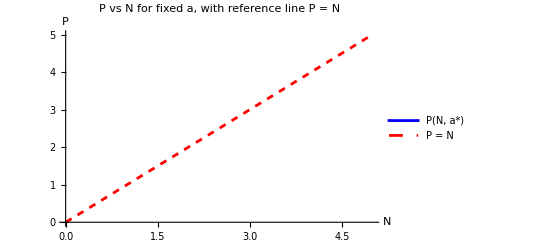

```mathematica
Plot[{Pfunc[N],N},{N,0,5},PlotStyle->{Blue,{Red,Dashed}},PlotLegends->{"P(N) via astar","P = N"},AxesLabel->{"N","P"}]
```

ReplaceAll::reps: {-1.27778+1.50802/(-0.13649+√(-0.0400011+Power[«2»])+0.0972 n)^(1/3)+4.40945 (-0.13649+√(-0.0400011+Power[«2»])+0.0972 n)^(1/3)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-1.27778+1.54652/(-0.140285+√(-0.043143+Power[«2»])+0.0972 n)^(1/3)+4.40945 (-0.140285+√(-0.043143+Power[«2»])+0.0972 n)^(1/3)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-1.27778+1.58501/(-0.144079+√(-0.0464453+Power[«2»])+0.0972 n)^(1/3)+4.40945 (-0.144079+√(-0.0464453+Power[«2»])+0.0972 n)^(1/3)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Plot::invregion: (True&)[Identity[#1],Identity[#2]]& must be a Boolean function.

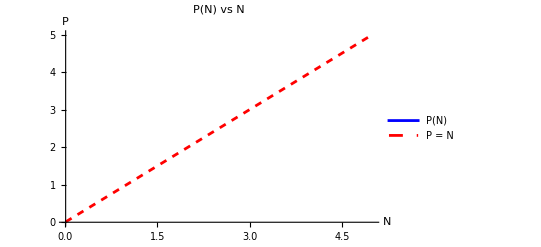

```mathematica
Plot[{P[N],N},{N,0.01,5},PlotLabel->"P(N) vs N",AxesLabel->{"N","P"},PlotStyle->{Blue,{Red,Dashed}},PlotLegends->{"P(N)","P = N"}]
```